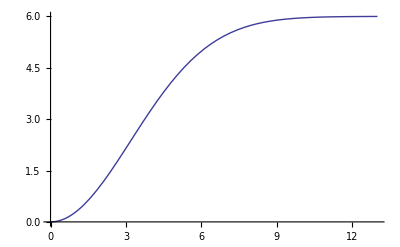

```mathematica
Subscript[σ, r]=4.5;Subscript[τ, r]=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
Subscript[τ, h]=1;B=1;G=0.2;
z[r_]=A(1-ⅇ^(-(r/Subscript[σ, r])^2));Plot[z[r],{r,0,13}]
```

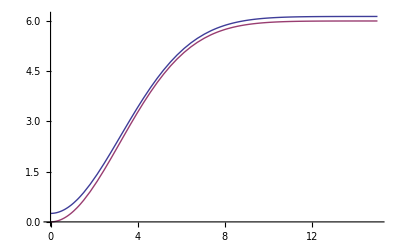

-Graphics3D-

```mathematica
h=F*Subscript[ϱ, r] +K*Subscript[ϱ, s]*Laplacian[z[r],{r,θ,z},"Cylindrical"];
H=(F*Subscript[ϱ, r])/G +(K*Subscript[ϱ, s])/G*Laplacian[z[r],{r,θ,z},"Cylindrical"](1-ⅇ^(-t/τ));
Plot[{h+z[r],z[r]},{r,0,15}]
Plot3D[H,{r,0,15},{t,0,10}]
```

```mathematica
ClearAll;
Subscript[σ, r]=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
z[r_,t_]:=ⅇ^(-(r/Subscript[σ, r])^2)ⅇ^(-t/τ)
eqn1=(Subscript[ϱ, s]-Subscript[ϱ, r])p'[t]+G*p[t]==Subscript[ϱ, r]/τ z[r,t]+K*Subscript[ϱ, s]*Laplacian[z[r,t],{r,θ,z},"Cylindrical"];
eqn2=p'[0]==0;
eqn3=p[0]==1;
DSolve[{eqn1},p[t],t]
```

{{p[t]→-0.999412 ⅇ^(-0.0493827 r^2-1. t) (-1.58822-5.73801×10^-7 r^2)+ⅇ^(0.000588235 t) C[1]}}

```mathematica
{{p[t]->-0.9994121105232218 ⅇ^(-0.04938271604938271 r^2-0.9999999999999999 t) (-1.5882236746550475-5.738006222150496*^-7 r^2)+ⅇ^(0.0005882352941176471 t) C[1]}}⟦1,1,2⟧
```

```mathematica
-0.9994121105232218 ⅇ^(-0.04938271604938271 r^2-0.9999999999999999 t) (-1.5882236746550475-5.738006222150496*^-7 r^2)+ⅇ^(0.0005882352941176471 t)
```

ⅇ^(0.000588235 t)-0.999412 ⅇ^(-0.0493827 r^2-1. t) (-1.58822-5.73801×10^-7 r^2)

```mathematica
ClearAll;
```

```mathematica
σ=4.5;τ=1;ρ=1000;ϱ=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
Clear[σ,τ,B,G,K,p,ρ,ϱ,p];
σ=4.5;τ=1;ρ=1000;ϱ=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))
eqn1=(ρ-ϱ)D[p[r,t], t]-G*p[r,t]==ϱ D[z[r,t], t]+K*ρ*Laplacian[z[r,t],{r,θ,z},"Cylindrical"];
eqn2=D[p[r,t], t]==-M*p[r,t];
sol=DSolve[{eqn1},p[r,t],{r,t}]
a=sol⟦1,1,2⟧/.C[1][r]->1
```

{{p[r,t]→ⅇ^(-0.0493827 r^2-1. t) (-9.53509+3.44483×10^-6 r^2+ⅇ^t (-0.118519+0.00585277 r^2))+ⅇ^(-0.000588235 t) C[1][r]}}

ⅇ^(-0.000588235 t)+ⅇ^(-0.0493827 r^2-1. t) (-9.53509+3.44483×10^-6 r^2+ⅇ^t (-0.118519+0.00585277 r^2))

```mathematica
Clear[L,M,P,A,h];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;

L=(Subscript[ϱ, s]-Subscript[ϱ, r])/G;M=Subscript[ϱ, r]/G;P=(K*Subscript[ϱ, s])/G;
Clear[L,M,P,A,h,τ,σ];

z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))
z[r_]:=-A*ⅇ^(-r^2)
sol=DSolve[L*D[h[r,t], t]==-M*D[z[r,t], t]+P*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]-h[r,t],{h[r,t]},{r,t}];
h=sol⟦1,1,2⟧/.C[1][r]->f[r];
g=DSolve[P*Laplacian[z[r],{r,θ,z},"Cylindrical"]==h,f[r],r]⟦1,1,2⟧;
h1=g/.f[r]->g;
Simplify[h]
Simplify[h1]
(* FullSimplify[sol⟦1,1,2⟧/.C[1][r]->1] *)
```

(A ⅇ^(-r^2/σ^2-t/τ) (M σ^4+4 P (r^2-σ^2) τ-4 ⅇ^(t/τ) P (r^2-σ^2) (-L+τ)))/(σ^4 (-L+τ))+ⅇ^(-t/L) f[r]

-ⅇ^(t/L) (4 A ⅇ^(-r^2) P (-1+r^2)+(A ⅇ^(-r^2/σ^2-t/τ) (M σ^4+4 P (r^2-σ^2) τ-4 ⅇ^(t/τ) P (r^2-σ^2) (-L+τ)))/(σ^4 (-L+τ)))

```mathematica
σ=4.5;τ=10000;ρ=1000;ϱ=2700;K=0.0001;F=50*10^(-6);A=6;B=1;G=1;
L=(Subscript[ϱ, s]-Subscript[ϱ, r])/G;M=Subscript[ϱ, r]/G;P=(K*Subscript[ϱ, s])/G;
```

```mathematica
Clear[L,M,P,A,h];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;

L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H];

z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)*(1-ⅇ^-t)
Q:=G *P*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]-H

sol=DSolve[L*D[h[r,t], t]==-M D[z[r,t], t]+P*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]-Q,{h[r,t]},{r,t}] 

h=sol⟦1,1,2⟧/.C[1][r]->f[r,t]
g=DSolve[Q==h,f[r,t],{r,t}]⟦1,1,2⟧

h1=h/.f[r,t]->g
(*
Simplify[h]
Simplify[h1]
*)
```

{{h[r,t]→(ⅇ^(-t-r^2/σ^2) (ⅇ^(t+r^2/σ^2) H t σ^4+A (-M σ^4+4 (-1+G) P (1+ⅇ^t t) (r^2-σ^2))))/(L σ^4)+C[1][r]}}

(ⅇ^(-t-r^2/σ^2) (ⅇ^(t+r^2/σ^2) H t σ^4+A (-M σ^4+4 (-1+G) P (1+ⅇ^t t) (r^2-σ^2))))/(L σ^4)+f[r,t]

-1/(L σ^4)ⅇ^(-t-r^2/σ^2) (-4 A P r^2+4 A G P r^2-4 A G L P r^2+4 A ⅇ^t G L P r^2-4 A ⅇ^t P r^2 t+4 A ⅇ^t G P r^2 t+4 A P σ^2-4 A G P σ^2+4 A G L P σ^2-4 A ⅇ^t G L P σ^2+4 A ⅇ^t P t σ^2-4 A ⅇ^t G P t σ^2+ⅇ^(t+r^2/σ^2) H L σ^4-A M σ^4+ⅇ^(t+r^2/σ^2) H t σ^4)

-1/(L σ^4)ⅇ^(-t-r^2/σ^2) (-4 A P r^2+4 A G P r^2-4 A G L P r^2+4 A ⅇ^t G L P r^2-4 A ⅇ^t P r^2 t+4 A ⅇ^t G P r^2 t+4 A P σ^2-4 A G P σ^2+4 A G L P σ^2-4 A ⅇ^t G L P σ^2+4 A ⅇ^t P t σ^2-4 A ⅇ^t G P t σ^2+ⅇ^(t+r^2/σ^2) H L σ^4-A M σ^4+ⅇ^(t+r^2/σ^2) H t σ^4)+(ⅇ^(-t-r^2/σ^2) (ⅇ^(t+r^2/σ^2) H t σ^4+A (-M σ^4+4 (-1+G) P (1+ⅇ^t t) (r^2-σ^2))))/(L σ^4)

```mathematica
Clear[L,M,P,A,h,z];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H,K,u,q,z];

z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)+u[r] ⅇ^(-t/τ)

DSolve[K*Laplacian[z[r],{r,θ,z},"Cylindrical"]==-L*q[r],q[r],r] ;
q[r]=First[Evaluate[q[r]/.%]]
```

(4 A ⅇ^(-r^2/σ^2) K (r^2-σ^2))/(L σ^4)

```mathematica
DSolve[K*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]==D[z[r,t], t]-L*q[r],u[r],r]
```

{{u[r]→0}}

```mathematica
z[r,t]=z[r,t]/.u[r]->u[r]/.%
```

```mathematica
h=sol⟦1,1,2⟧/.C[1][r]->f[r,t]
g=DSolve[Q==h,f[r,t],{r,t}]⟦1,1,2⟧

h1=h/.f[r,t]->g
```

```mathematica
Clear[L,M,P,A,h,z];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H,K,u,q,z];

z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)+u[r] ⅇ^(-t/τ)

DSolve[K*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]==0,u[r],{r}] 
u[r]=First[Evaluate[u[r]/.%]]/.C[1]->1;
u[r]=u[r]/.C[2]->1
```

{{u[r]→A ⅇ^(-r^2/σ^2+t/τ)+C[2]+C[1] Log[r]}}

1+A ⅇ^(-r^2/σ^2+t/τ)+Log[r]

```mathematica
Clear[L,M,P,A,h,z];
σ=4.5;τ=1;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=50*10^(-6);A=6;
L=Subscript[ϱ, s]-Subscript[ϱ, r];M=Subscript[ϱ, r];P=K*Subscript[ϱ, s];G=0.2;H=0.5*Subscript[ϱ, r];
Clear[L,M,P,A,h,τ,σ,k,R,S,f,l,G,H,K,u,q,z];
K=0.0001;G=1;A=6;σ=4;τ=10000;

z[r_]:=-A*ⅇ^(-(r/σ)^2)
z[r_,t_]:=-A*ⅇ^(-(r/σ)^2)(1-ⅇ^(-t/τ))
dz[r_,t_]:=D[z[r,t], t]

Solve[K*Laplacian[z[r,t],{r,θ,z},"Cylindrical"]==G D[z[r,t], t]-q[r,t],q[r,t],{r,t}] ;

q[r_,t_]=Simplify[First[Evaluate[q[r,t]/.%]]]
z[r,t]
```

ⅇ^(-0.0625 r^2-0.0001 t) (-0.00045-9.375×10^-6 r^2+ⅇ^(0.0001 t) (-0.00015+9.375×10^-6 r^2))

-6 ⅇ^(-r^2/16) (1-ⅇ^(-t/10000))

```mathematica
Manipulate[Plot[{q[r,t]},{r,0,14}],{t,0,100000},PlotRange->{-0.00020,0.00010}]
```

```mathematica
Manipulate[Plot[{z[r,t]},{r,0,14}],{t,0,10000}]
```

```mathematica
Manipulate[Plot[{dz[r,t]},{r,0,14}],{t,0.1,100000}]
```